```mathematica
Nt = 512;(*512*) 
ti = 0; tf = 5; 
deltat = (tf - ti) /Nt ;
Nx = 128;(*128*)
xi = -40; xf = 40; 
deltax = (xf - xi) / Nx; 
c =  1;

(*For Max Eigenvalue Plots*)
rs = Table[0.1*i,{i,1,100}];(*200 for Limits*)

maxevalsLD2 = Table[0,{i,1,Length[rs]}];
maxevalsRK3 = Table[0,{i,1,Length[rs]}];
maxevalsPI = Table[0,{i,1,Length[rs]}];



Subscript[δ, i_,j_]:=KroneckerDelta[i,j];

selectwidth = 5;
diffOrder = 5;
deriv = 2;


(*The total number of points in the stencil*)
totalpoints = (2*selectwidth) + 1;

(*The middle point in the stencil*)
middlepoint = selectwidth + 1;

(*Set up the grid for the stencil*)
grid=x0+(Range[totalpoints]-middlepoint)Δx;

(LP=NDSolve`FiniteDifferenceDerivative[Derivative[deriv],grid,"DifferenceOrder"->diffOrder]@"DifferentiationMatrix"//Normal);
(LP2=NDSolve`FiniteDifferenceDerivative[Derivative[4],grid,"DifferenceOrder"->diffOrder - 2]@"DifferentiationMatrix"//Normal);

(*define r:=Δt/(Δx^deriv)*)
r=.;
LPX = LP*((-1)^deriv)*(r*(Δx)^deriv);
LPX2 = LP2*((-1)^4)*(r*(Δx)^4);
LPX3 = LP3*((-1)^6)*(r*(Δx)^6);

gn = (LPX[[middlepoint,All]]//Normal)//Simplify//FullSimplify;
LPX = Table[RotateRight[gn,i],{i,-selectwidth,selectwidth}];
LPX[[1,-1]]=0;
LPX[[1,-2]]=0;
LPX[[2,-1]]=0;
LPX[[-1,1]]=0;
LPX[[-1,2]]=0;
LPX[[-2,1]]=0;
LPX[[-3,1]] = 0;
LPX[[-2,2]] = 0;
LPX[[-1,3]] = 0;
LPX[[1,-3]] = 0;
LPX[[2,-2]] = 0;
LPX[[3,-1]] = 0;

gn2 = (LPX2[[middlepoint,All]]//Normal)//Simplify//FullSimplify;
LPX2 = Table[RotateRight[gn2,i],{i,-selectwidth,selectwidth}];
LPX2[[1,-1]]=0;
LPX2[[1,-2]]=0;
LPX2[[2,-1]]=0;
LPX2[[-1,1]]=0;
LPX2[[-1,2]]=0;
LPX2[[-2,1]]=0;
LPX2[[-3,1]] = 0;
LPX2[[-2,2]] = 0;
LPX2[[-1,3]] = 0;
LPX2[[1,-3]] = 0;
LPX2[[2,-2]] = 0;
LPX2[[3,-1]] = 0;


IP=IdentityMatrix[Length[LPX]];

(Mn=Inverse[IP-(ⅈ * LPX)/4  - LPX2/48 ].(IP+(ⅈ * LPX)/4- LPX2/48));


fn=(Mn[[middlepoint,All]]//Normal)//Simplify//FullSimplify;

(*Generate a M Matrix from the L matrix for the stencil*)
MP = Table[0,{i,1,Nx},{j,1,Nx}];

(*WITHOUT Periodic Boundary Conditions Placed*)
MP = Table[Sum[(Subscript[δ, i,j+(middlepoint-k)])fn[[k]] + (Subscript[δ, i,(j-k)])fn[[middlepoint + k]],{k,selectwidth}] + Subscript[δ, i,j] fn[[middlepoint]],{i,1,Nx},{j,1,Nx}];

(*WITH Periodic Boundary Conditions*)
(*MP = Table[Sum[(Subscript[δ, i,j+(middlepoint-k)])fn[[k]] + (Subscript[δ, i,(j-k)])fn[[middlepoint + k]],{k,selectwidth}] + Subscript[δ, i,j] fn[[middlepoint]] + Sum[(Subscript[δ, (i + Nx) - n,j])fn[[selectwidth - (n - 1)]] + (Subscript[δ, (i + Nx) + n,(j + 2*Nx)])fn[[(middlepoint + 1) + (n - 1)]]  ,{n,1,selectwidth}],{i,1,Nx},{j,1,Nx}];*)
```

```mathematica
Do[
deltat = (deltax^2) * rs[[p]];

Xp= N[Table[xm = xi + m *deltax, {m, 0, Nx}],32];

T = N[Table[tn = ti + n *deltat, {n, 0, Nt -1 }],32];
Xo = N[Table[xn = xi + n *deltax, {n, 0, Nx -1}],32];

f[x_] = ⅇ^(- x^2+ⅈ x);


(************************************************************************************************************************)
(*Differentiation Matrix*)
(************************************************************************************************************************)
L1 = N[(NDSolve`FiniteDifferenceDerivative[Derivative[1],Xp,"DifferenceOrder"->1, PeriodicInterpolation->True]@"DifferentiationMatrix"//Normal),32];
L1//MatrixForm;
DL1 = N[-c * L1 * deltat,32];

L2 = N[Table[(NDSolve`FiniteDifferenceDerivative[Derivative[i],Xp, "DifferenceOrder"->2, PeriodicInterpolation->True]@"DifferentiationMatrix"//Normal), {i,1,8}],32];
DL2 = L2[[2]] * deltat * (ⅈ / 2);
DL4 = L2[[4]] * (deltat * (ⅈ / 2))^2;
DL6 = L2[[6]] * (deltat * (ⅈ / 2))^3;


(* LD2 *)
ILD2 = N[IdentityMatrix[Length[DL2]],32];
ALD2 = N[ILD2 - (DL2 / 2),32];
BLD2 = N[ILD2 + (DL2 / 2),32];
MLD2 = N[Inverse[ALD2].BLD2,32];

evals = Eigenvalues[N[MLD2]];

maxevalsLD2[[p]] = Max[Abs[evals]];


(*RK3*)
IRK3 = N[IdentityMatrix[Length[DL2]],32];

MRK3 = N[(IRK3 + (DL2) + ((1/2)*(DL4))) +  ((1/6) * (DL6)),32];

evalsRK3 = Eigenvalues[N[MRK3]];

maxevalsRK3[[p]] = Max[Abs[evalsRK3]];

(*PI*)
MPtest = N[MP//.{N[r -> rs[[p]],32]},32];

evalsPI = Eigenvalues[N[MPtest]];

maxevalsPI[[p]] = Max[Abs[evalsPI]];

Print["Finished "<>ToString[rs[[p]]]];


,{p,1,Length[rs]}]
```

Finished 0.1

Finished 0.2

Finished 0.3

Finished 0.4

Finished 0.5

Finished 0.6

Finished 0.7

Finished 0.8

Finished 0.9

Finished 1.

Finished 1.1

Finished 1.2

Finished 1.3

Finished 1.4

Finished 1.5

Finished 1.6

Finished 1.7

Finished 1.8

Finished 1.9

Finished 2.

Finished 2.1

Finished 2.2

Finished 2.3

Finished 2.4

Finished 2.5

Finished 2.6

Finished 2.7

Finished 2.8

Finished 2.9

Finished 3.

Finished 3.1

Finished 3.2

Finished 3.3

Finished 3.4

Finished 3.5

Finished 3.6

Finished 3.7

Finished 3.8

Finished 3.9

Finished 4.

Finished 4.1

Finished 4.2

Finished 4.3

Finished 4.4

Finished 4.5

Finished 4.6

Finished 4.7

Finished 4.8

Finished 4.9

Finished 5.

Finished 5.1

Finished 5.2

Finished 5.3

Finished 5.4

Finished 5.5

Finished 5.6

Finished 5.7

Finished 5.8

Finished 5.9

Finished 6.

Finished 6.1

Finished 6.2

Finished 6.3

Finished 6.4

Finished 6.5

Finished 6.6

Finished 6.7

Finished 6.8

Finished 6.9

Finished 7.

Finished 7.1

Finished 7.2

Finished 7.3

Finished 7.4

Finished 7.5

Finished 7.6

Finished 7.7

Finished 7.8

Finished 7.9

Finished 8.

Finished 8.1

Finished 8.2

Finished 8.3

Finished 8.4

Finished 8.5

Finished 8.6

Finished 8.7

Finished 8.8

Finished 8.9

Finished 9.

Finished 9.1

Finished 9.2

Finished 9.3

Finished 9.4

Finished 9.5

Finished 9.6

Finished 9.7

Finished 9.8

Finished 9.9

Finished 10.

```mathematica
maxevalsLD2 = Join[{1},maxevalsLD2];
rsLD2 = Join[{0},rs];

maxevalsPI = Join[{1},maxevalsPI];
rsPI = Join[{0},rs];

maxevalsRK3 = Join[{1},maxevalsRK3];
rsRK3 = Join[{0},rs];
```

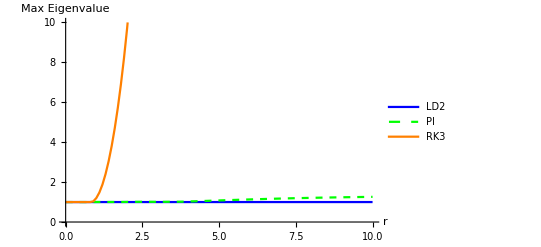

```mathematica
ListLinePlot[{Transpose[{rsLD2,maxevalsLD2}],Transpose[{rsPI,maxevalsPI}],Transpose[{rsRK3,maxevalsRK3}]},PlotStyle->{Blue, {Green, Dashed}, Orange}, PlotLegends->{"LD2", "PI", "RK3"}, AxesLabel->{"r", "Max Eigenvalue"}, PlotRange->{{0,10},{0,10}}]
```

```mathematica
exportData=Flatten/@Transpose[{rsLD2,maxevalsLD2, maxevalsPI, maxevalsRK3}];
Export["C:\\Users\\eagle\\Desktop\\SPIN_Research_Report\\eigenvalues.dat",exportData,"Table"];
```

```mathematica
differencesPI = Table[0,{i,2,Length[maxevalsPI]}];
Do[
differencesPI[[i - 1]] = Abs[maxevalsPI[[i]] - maxevalsPI[[i-1]]];
,{i,2,Length[maxevalsPI]}]
```

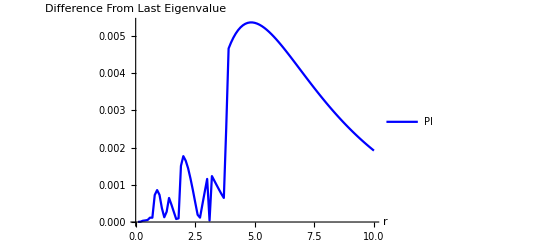

```mathematica
ListLinePlot[{Transpose[{rs,differencesPI}]},PlotStyle->{Blue, {Green, Dashed}, Red}, PlotLegends->{"PI", "New"}, AxesLabel->{"r", "Difference From Last Eigenvalue"},PlotRange->All]
```